```mathematica
soliton[x_,alfa_,z_]:=Sqrt[1/-alfa]Sech[Sqrt[2]*(x-z)]
```

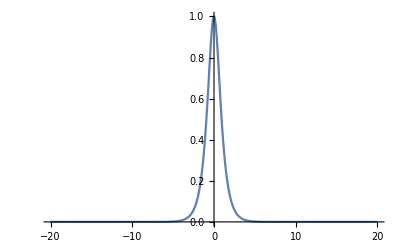

```mathematica
Plot[soliton[x,-1,0],{x,-20,20}, PlotRange->All]
```

```mathematica
f[ω_]:=FourierTransform[soliton[x,-1,0],x,ω]
```

```mathematica
f[g] /.g->4
```

1/2 √π Sech[√2 π]

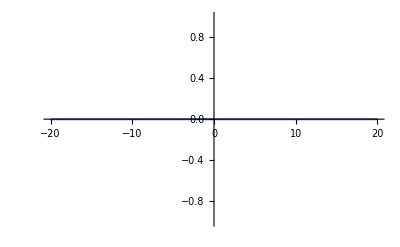

```mathematica
Plot[f[ω]/.ω->x,{x,-20,20}, PlotRange->All]
```

```mathematica
Needs["FourierSeries`"]




f1[t_]:=UnitStep[1-t] UnitStep[t+1]
```

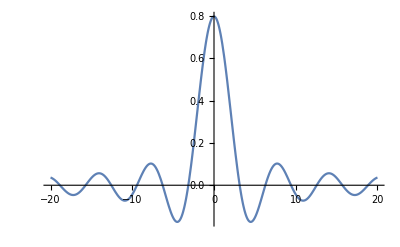

```mathematica
Plot[NFourierTransform[f1[t],t,ω]/.ω->x,{x,-20,20},PlotRange->All]
```

NIntegrate::deorel: The relative error 3.87829×10^6 is larger than expected for the integrand 1. Cos[19.9992 t] Sech[√2 Abs[0.-t]] over {0,∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10,5}.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand 1. Cos[19.9992 t] Sech[√2 Abs[0.-t]] over {0,∞}. DoubleExponentialOscillatory obtained -5.1053×10^-8 and 3.87829×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-12.8408}. NIntegrate obtained 5.00688×10^-10 and 3.1243×10^-11 for the integral and error estimates.

NIntegrate::deorel: The relative error 3.87829×10^6 is larger than expected for the integrand 1. Cos[19.9992 t] Sech[√2 (0.+t)] over {0,∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10,5}.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand 1. Cos[19.9992 t] Sech[√2 (0.+t)] over {0,∞}. DoubleExponentialOscillatory obtained -5.1053×10^-8 and 3.87829×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {12.8408}. NIntegrate obtained 5.00688×10^-10 and 3.1243×10^-11 for the integral and error estimates.

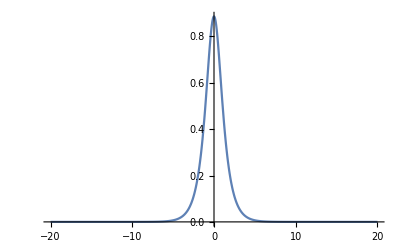

```mathematica
Plot[NFourierTransform[soliton[t,-1,0],t,ω]/.ω->x,{x,-20,20},PlotRange->All]
```